NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{m→426930.,p→0.000069164,q→0.200897}

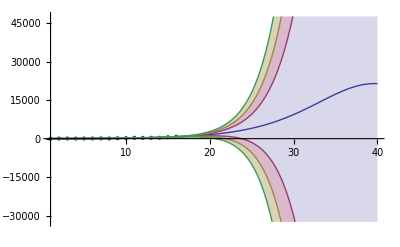

```mathematica
S[t_, m_, p_, q_] := m*((p+q)^2/p) *( Exp[-(p+q)*t]/(1+(q/p)*Exp[-(p+q)*t])^2);

data = {{1, 31},{2, 70},{3, 85},{4, 69},{5, 94},{6, 95},{7, 141},{8, 113},{9, 181},{10, 234},{11, 345},{12, 328},{13, 358},{14, 376},{15, 601},{16, 781}};

nlm=NonlinearModelFit[data,S[t, m, p, q],{m,p,  q},t];

params = nlm["BestFitParameters"]

{bands80[x_],bands90[x_],bands95[x_]}=Table[nlm["SinglePredictionBands",ConfidenceLevel->cl],{cl,{.5,.75,.9}}];

Show[
ListPlot[data, PlotRange->All],
Plot[{nlm[t],bands80[t],bands90[t],bands95[t]},{t,1,40},Filling->{2->{1},3->{2},4->{3}}]
]
```

```mathematica
(Log[0.3176]-Log[0.00153])/(0.3176-0.001)
```

16.8526